# Red blood cell metabolism

```mathematica
Quit[]
```

```mathematica
<<Toolbox`
<<Toolbox`Style`
```

## Construction and parameterization of a MASS model

```mathematica
glycolysis=constructModel[{Overscript[atp^c+glu^c⇌adp^c+g6p^c+h^c, vhk],Overscript[g6p^c⇌f6p^c, vpgi],Overscript[atp^c+f6p^c⇌adp^c+fdp^c+h^c, vpfk],Overscript[dhap^c⇌gap^c, vtpi],Overscript[fdp^c⇌dhap^c+gap^c, vald],Overscript[gap^c+nad^c+phos^c⇌h^c+nadh^c+pg13^c, vgapdh],Overscript[adp^c+pg13^c⇌atp^c+pg3^c, vpgk],Overscript[pg3^c⇌pg2^c, vpglm],Overscript[pg2^c⇌h2o^c+pep^c, veno],Overscript[adp^c+h^c+pep^c⇌atp^c+pyr^c, vpk],Overscript[h^c+nadh^c+pyr^c⇌lac^c+nad^c, vldh],(amp^c⇌∅)^vamp,Overscript[2 adp^c⇌amp^c+atp^c, vapk],(pyr^c⇌∅)^vpyr,(lac^c⇌∅)^vlac,Overscript[atp^c+h2o^c⇌adp^c+h^c+phos^c, vatp],Overscript[nadh^c⇌h^c+nad^c, vnadh],(∅⇌glu^c)^vgluin,(∅⇌amp^c)^vampin,(h^c⇌∅)^vh,(h2o^c⇌∅)^vh2o},Ignore->{h^c,h2o^c},UnitChecking->True];
```

```mathematica
setInitialConditions[glycolysis,{glu^c->1. Millimole Liter^-1,g6p^c->0.0486 Millimole Liter^-1,f6p^c->0.0198 Millimole Liter^-1,fdp^c->0.0146 Millimole Liter^-1,dhap^c->0.16 Millimole Liter^-1,gap^c->0.00728 Millimole Liter^-1,pg13^c->0.000243 Millimole Liter^-1,pg3^c->0.0773 Millimole Liter^-1,pg2^c->0.0113 Millimole Liter^-1,pep^c->0.017 Millimole Liter^-1,pyr^c->0.060301 Millimole Liter^-1,lac^c->1.36 Millimole Liter^-1,nad^c->0.0589 Millimole Liter^-1,nadh^c->0.0301 Millimole Liter^-1,amp^c->0.08672812499999999 Millimole Liter^-1,adp^c->0.29 Millimole Liter^-1,atp^c->1.6 Millimole Liter^-1,phos^c->2.5 Millimole Liter^-1,h^c->0.00008997573444801929 Millimole Liter^-1,h2o^c->1. Millimole Liter^-1}]
```

```mathematica
setParameters[glycolysis,{Underscript[K, vhk]->850,Underscript[K, vpgi]->0.41,Underscript[K, vpfk]->310,Underscript[K, vtpi]->0.05714285714285714,Underscript[K, vald]->0.082 Millimole Liter^-1,Underscript[K, vgapdh]->0.0179 Liter Millimole^-1,Underscript[K, vpgk]->1800,Underscript[K, vpglm]->0.14705882352941177,Underscript[K, veno]->1.6949152542372883,Underscript[K, vpk]->363000,Underscript[K, vldh]->26300,Underscript[K, vamp]->∞,Underscript[K, vapk]->1.65,Underscript[K, vpyr]->1.,Underscript[K, vlac]->1.,Underscript[K, vatp]->∞ Millimole Liter^-1,Underscript[K, vnadh]->∞,Underscript[K, vgluin]->∞(*K_vgluin->1.1*),Underscript[K, vampin]->∞,Underscript[K, vh]->1.,Underscript[K, vh2o]->1.,pyr^Xt->0.06 Millimole Liter^-1,amp^Xt->Millimole Liter^-1,h^Xt->0.00006309573444801929 Millimole Liter^-1,h2o^Xt->Millimole Liter^-1,glu^Xt->Millimole Liter^-1,lac^Xt->Millimole Liter^-1,p["Volume","c"]->1 Liter}]
```

```mathematica
basis=({
 {1, 0, 1},
 {1, 0, 0},
 {0, 1, 0}
}).NullSpace[glycolysis];
TableForm[basis.glycolysis["Fluxes"]]
```

v_vald+2 v_vatp+2 v_veno+2 v_vgapdh+v_vgluin+2 v_vh+v_vhk+2 v_vlac+2 v_vldh+v_vpfk+v_vpgi+2 v_vpgk+2 v_vpglm+2 v_vpk+v_vtpi
2 v_vh-v_vlac-v_vldh+v_vnadh+v_vpyr
v_vamp+v_vampin

```mathematica
solution={1.12,0.224,0.014}.basis;
steadyStateFluxes=#[[1]]->#[[2]]Millimole Liter^-1 Hour^-1&/@Thread[Rule[glycolysis["Fluxes"],solution]]
```

{v_vhk→1.12 Millimole Hour^-1 Liter^-1,v_vpgi→1.12 Millimole Hour^-1 Liter^-1,v_vpfk→1.12 Millimole Hour^-1 Liter^-1,v_vtpi→1.12 Millimole Hour^-1 Liter^-1,v_vald→1.12 Millimole Hour^-1 Liter^-1,v_vgapdh→2.24 Millimole Hour^-1 Liter^-1,v_vpgk→2.24 Millimole Hour^-1 Liter^-1,v_vpglm→2.24 Millimole Hour^-1 Liter^-1,v_veno→2.24 Millimole Hour^-1 Liter^-1,v_vpk→2.24 Millimole Hour^-1 Liter^-1,v_vldh→2.016 Millimole Hour^-1 Liter^-1,v_vamp→0.014 Millimole Hour^-1 Liter^-1,v_vapk→0. Millimole Hour^-1 Liter^-1,v_vpyr→0.224 Millimole Hour^-1 Liter^-1,v_vlac→2.016 Millimole Hour^-1 Liter^-1,v_vatp→2.24 Millimole Hour^-1 Liter^-1,v_vnadh→0.224 Millimole Hour^-1 Liter^-1,v_vgluin→1.12 Millimole Hour^-1 Liter^-1,v_vampin→0.014 Millimole Hour^-1 Liter^-1,v_vh→2.688 Millimole Hour^-1 Liter^-1,v_vh2o→0. Millimole Hour^-1 Liter^-1}

```mathematica
updateInitialConditions[glycolysis,steadyStateFluxes];
```

```mathematica
perc=calcPERC[glycolysis]/.Undefined->100000;
updateParameters[glycolysis,perc];
```

calcPERC::atequilibrium: Reaction "vapk" is either at equlibrium or not active. Forward rate constant k_StyleBox[ is set to Undefined (this value can be specified using the option "AtEquilibriumDefault").

calcPERC::atequilibrium: Reaction "vh2o" is either at equlibrium or not active. Forward rate constant k_StyleBox[ is set to Undefined (this value can be specified using the option "AtEquilibriumDefault").

adjustUnits::noUnitsProvidedRateConst: No units provided for k_StyleBox[. (InterpretationBox[)^(1 - rxnOrder)(InterpretationBox[)^(rxnOrder - 1)(InterpretationBox[)^-1 assumed: 100000 Liter Hour^-1 Millimole^-1

adjustUnits::noUnitsProvidedRateConst: No units provided for k_StyleBox[. (InterpretationBox[)^(1 - rxnOrder)(InterpretationBox[)^(rxnOrder - 1)(InterpretationBox[)^-1 assumed: 100000 Hour^-1

### Simulate the model

```mathematica
{concSol,fluxSol}=simulate[glycolysis,{t,0,100}];
```

### Visualize the time-course concentration and flux profiles

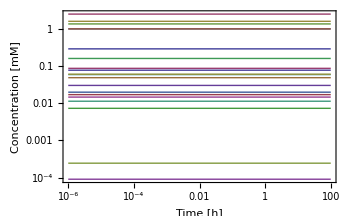

```mathematica
plotSimulation[concSol,FrameLabel->{"Time [h]","Concentration [mM]"}]
```

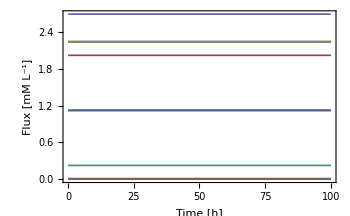

```mathematica
plotSimulation[fluxSol,PlotFunction->Plot,FrameLabel->{"Time [h]","Flux [mM L^-1]"}]
```

### Perturb the model and analyze the dynamic consequences

Some text here ...

```mathematica
{concSol,fluxSol}=simulate[glycolysis,{t,0.,1000},Events->{"Glucose pulse"->WhenEvent[t==1,m["glu","c"][t]->2Millimole Liter^-1]}];
```

Visualize the time-course profiles of concentrations, fluxes, and Atkins and Redox energy charges.

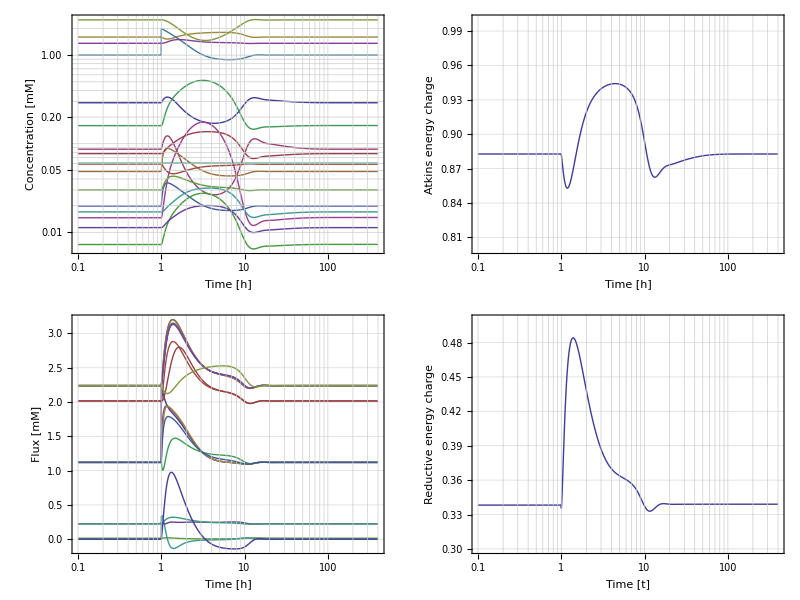

```mathematica
padding={{Scaled[0.035],Scaled[0.01]},{Automatic,Automatic}};
opts={ImagePadding->padding,GridLines->Automatic,GridLinesStyle->GrayLevel[.8]};
Grid[
{{plotSimulation[FilterRules[concSol,Except[{h^c,h2o^c,m["pg13","c"]}]],{t,0.1,400},FrameLabel->{"Time [h]","Concentration [mM]"},Sequence@@opts],plotSimulation[{"Atkins energy charge"->(adp^c/2+atp^c)/(adp^c+amp^c+atp^c)}/.concSol,{t,0.1,400},PlotFunction->LogLinearPlot,PlotRange->{All,{0.8,1.}},FrameLabel->{"Time [h]","Atkins energy charge"},Sequence@@opts]},
{plotSimulation[FilterRules[fluxSol,Except[{v["vh"]}]],{t,0.1,400},FrameLabel->{"Time [h]","Flux [mM]"},PlotFunction->LogLinearPlot,Sequence@@opts],
plotSimulation[{"Redox charge"->nadh^c/(nad^c+nadh^c)}/.concSol,{t,0.1,400},FrameLabel->{"Time [t]","Reductive energy charge"},PlotFunction->LogLinearPlot,PlotRange->{All,{0.3,0.5}},Sequence@@opts]}}
]
AutoCollapse[]
```

Let’s draw an animation of ...

```mathematica
nodeMapFrames=Table[Grid@Partition[Show[#,ImageSize->300]&/@filter[drawNodeMaps[glycolysis,Fluxes->Chop@stripUnits[fluxSol],Legend->False,PlotLabel->False],{h^c,adp^c,atp^c,amp^c,h2o^c,nad^c,nadh^c,pyr^c,dhap^c}][[All,2]],3],{t,1,15}];
```

```mathematica
ListAnimate[nodeMapFrames]
```

## Coupling pathways

### Combining individual pathway models

Load the glycolysis, pentose phosphate, nucleotide salvage pathways:

```mathematica
glycolysis=ExampleData[{"Toolbox","Glycolysis"}];
ppp=ExampleData[{"Toolbox","PentosePhosphatePathway"}];
salvage=ExampleData[{"Toolbox","NucleotideSalvagePathway"}];
hemoglobin=ExampleData[{"Toolbox","Hemoglobin"}];
```

Set operations like Intersection, Complement etc. can be applied to models. In this case we’ll use the Union function to merge the three pathways and get rid of redundant reactions. Models take precedence from left to right in terms of parameters, initial conditions, and other model attributes.

```mathematica
combi=Union[glycolysis,ppp,salvage,hemoglobin];
```

We can remove a few obsolete reaction using the deleteReactions function (remember that structural operations do not change the model in-place):

```mathematica
combi=deleteReactions[combi,{"EX_g6p_c","EX_f6p_c","EX_gap_c","EX_h_c","EX_h2o_c","EX_r5p_c","vamp","vampin","vatpgen"}];
```

The merged model contains 40 metabolites and 46 reactions:

```mathematica
combi//Dimensions
```

{48,53}

The merged model is not in a steady-state:

```mathematica
{concSol,fluxSol}=simulate[combi,{t,0,1*^6}];
```

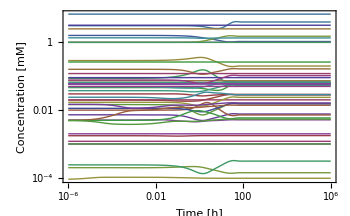

```mathematica
plotSimulation[concSol,FrameLabel->{"Time [h]","Concentration [mM]"}]
```

### Steady-state relaxation: option 1

```mathematica
combiRelaxed=combi;
updateConstraints[combiRelaxed,v[getID[#]]->{-∞,∞}&/@getExchanges[combi]]
updateParameters[combiRelaxed,{Keq["vh2o"]->0.9,Keq["vtki"]->3}]
```

```mathematica
fbaSol=Chop@fba[combiRelaxed,Subscript[v, vhk],{Subscript[v, vhk]->{1.12,1.12},Subscript[v, vak]->{0.12,0.12},Subscript[v, vg6pdh]->{0.21,0.21},Subscript[v, vpfk]->{1.05,1.05},Subscript[v, vpgi]->{0.91,0.91},Subscript[v, vdpgm]->{0.441,0.441},Subscript[v, vprppsyn]->{0.014,0.014},Subscript[v, vada]->{0.01,0.01},v["vado"]->{-0.01,-0.01},v["vapk"]->{0.,0.},v["vnadh"]->{1.12*0.2,1.12*0.2}}];
newSSfluxes=#[[1]]->#[[2]]Millimole Hour^-1&/@fbaSol;
updateInitialConditions[combiRelaxed,newSSfluxes];
perc=SortBy[Quiet[calcPERC[combiRelaxed],{calcPERC::atequilibrium,calcPERC::ZeroKeq}],Last];
perc=updateRules[perc,FilterRules[hemoglobin["Parameters"],_rateconst]]/.Undefined->100000;
updateParameters[combiRelaxed,perc];
```

adjustUnits::noUnitsProvidedRateConst: No units provided for k_StyleBox[. (InterpretationBox[)^(1 - rxnOrder)(InterpretationBox[)^(rxnOrder - 1)(InterpretationBox[)^-1 assumed: 100000 Liter Hour^-1 Millimole^-1

adjustUnits::noUnitsProvidedRateConst: No units provided for k_StyleBox[. (InterpretationBox[)^(1 - rxnOrder)(InterpretationBox[)^(rxnOrder - 1)(InterpretationBox[)^-1 assumed: 100000 Hour^-1

Comparing the initial conditions of the individual pathways with the newly obtained steady state reveals that fluxes and concentration are not dramatically different:

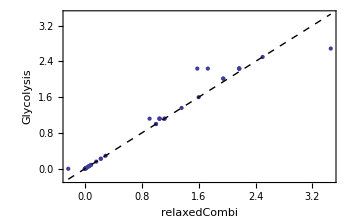

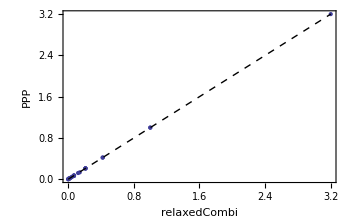

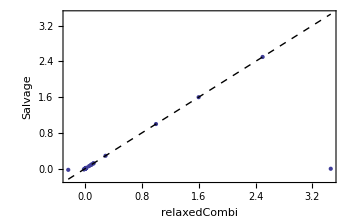

```mathematica
comparisonPlot=Show[ListPlot[Thread[Tooltip[#[[All,2]],#[[All,1]]]],##2],Graphics[{Dashed,Line[{{Min[#[[All,2]]],Min[#[[All,2]]]},{Max[#[[All,2]]],Max[#[[All,2]]]}}]}],PlotRange->Automatic]&;
comparisonPlot[stripUnits[scatterFromDicts[combiRelaxed["InitialConditions"],glycolysis["InitialConditions"]]],FrameLabel->{"relaxedCombi","Glycolysis"}]
comparisonPlot[stripUnits[scatterFromDicts[combiRelaxed["InitialConditions"],ppp["InitialConditions"]]],FrameLabel->{"relaxedCombi","PPP"}]
comparisonPlot[stripUnits[scatterFromDicts[combiRelaxed["InitialConditions"],salvage["InitialConditions"]]],FrameLabel->{"relaxedCombi","Salvage"}]
AutoCollapse[]
```

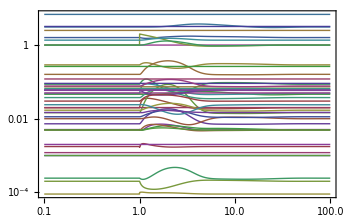

```mathematica
{concSol,fluxSol}=simulate[combiRelaxed,{t,.1,100},Events->{"Glucose pulse"->WhenEvent[t==1,glu^c[t]->2Millimole Liter^-1]}];
plotSimulation[concSol]
```

### Relaxation: option 2

We could set a new steady-state flux state and recalculate all PERCs etc. or we could just determine the steady-state the system relaxes to and use it as our new initial conditions for the merge model:

```mathematica
{concSol,fluxSol}=simulate[combi,{t,0,1*^6}];
```

```mathematica
plotSimulation[concSol,FrameLabel->{"Time [h]","Concentration [mM]"}]
```

-Graphics-

```mathematica
newSS=Flatten[{concSol,fluxSol}]/.t->1*^6;
combiRelaxed2=combi;
updateInitialConditions[combiRelaxed2,newSS];
perc=SortBy[Quiet[calcPERC[combiRelaxed2],{calcPERC::atequilibrium,calcPERC::ZeroKeq}],Last];
perc=updateRules[perc,FilterRules[hemoglobin["Parameters"],_rateconst]]/.Undefined->100000;
updateParameters[combiRelaxed2,perc];
```

adjustUnits::noUnitsProvidedRateConst: No units provided for k_StyleBox[. (InterpretationBox[)^(1 - rxnOrder)(InterpretationBox[)^(rxnOrder - 1)(InterpretationBox[)^-1 assumed: 100000 Liter Hour^-1 Millimole^-1

adjustUnits::noUnitsProvidedRateConst: No units provided for k_StyleBox[. (InterpretationBox[)^(1 - rxnOrder)(InterpretationBox[)^(rxnOrder - 1)(InterpretationBox[)^-1 assumed: 100000 Hour^-1

The merged model with the new initial conditions is in a steady-state:

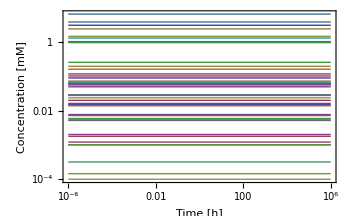

```mathematica
plotSimulation[simulate[combiRelaxed2,{t,0,1*^6}][[1]],FrameLabel->{"Time [h]","Concentration [mM]"}]
```

```mathematica
{"E.C."->(adp^c/2+atp^c)/(adp^c+amp^c+atp^c),"Redox"->nadh^c/(nad^c+nadh^c),"Redox2"->nadph^c/(nadp^c+nadph^c)}/.combi
{"E.C."->(adp^c/2+atp^c)/(adp^c+amp^c+atp^c),"Redox"->nadh^c/(nad^c+nadh^c),"Redox2"->nadph^c/(nadp^c+nadph^c)}/.combiRelaxed
{"E.C."->(adp^c/2+atp^c)/(adp^c+amp^c+atp^c),"Redox"->nadh^c/(nad^c+nadh^c),"Redox2"->nadph^c/(nadp^c+nadph^c)}/.combiRelaxed2
```

{E.C.→0.882772,Redox→0.338202,Redox2→0.99697}

{E.C.→0.882772,Redox→0.338202,Redox2→0.99697}

{E.C.→0.876865,Redox→0.326867,Redox2→0.997853}

Comparing the initial conditions of the individual pathways with the newly obtained steady state reveals that fluxes and concentration are not dramatically different:

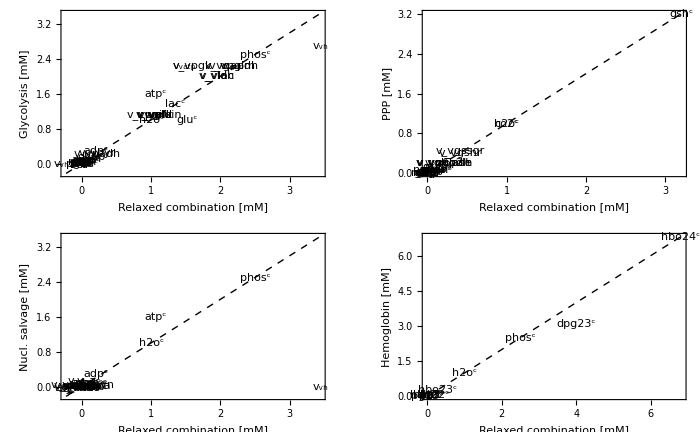

```mathematica
comparisonPlot=Show[Graphics[Text[#[[1]],#[[2]]]&/@#,Frame->True,##2,AspectRatio->1/GoldenRatio,PlotRange->All,ImagePadding->{{Scaled[0.15],Scaled[0.015]},{Automatic,Automatic}}],Graphics[{Dashed,Line[{{Min[#[[All,2]]],Min[#[[All,2]]]},{Max[#[[All,2]]],Max[#[[All,2]]]}}]}],BaseStyle->{FontFamily->"Helvetica",FontSize->12}]&;
GraphicsGrid[Partition[
{comparisonPlot[stripUnits[scatterFromDicts[combiRelaxed2["InitialConditions"],glycolysis["InitialConditions"]]],FrameLabel->{"Relaxed combination [mM]","Glycolysis [mM]"}],
comparisonPlot[stripUnits[scatterFromDicts[combiRelaxed2["InitialConditions"],ppp["InitialConditions"]]],FrameLabel->{"Relaxed combination [mM]","PPP [mM]"}],
comparisonPlot[stripUnits[scatterFromDicts[combiRelaxed2["InitialConditions"],salvage["InitialConditions"]]],FrameLabel->{"Relaxed combination [mM]","Nucl. salvage [mM]"}],
comparisonPlot[stripUnits[scatterFromDicts[combiRelaxed2["InitialConditions"],hemoglobin["InitialConditions"]]],FrameLabel->{"Relaxed combination [mM]","Hemoglobin [mM]"}]},2],ImageSize->350*2]
```

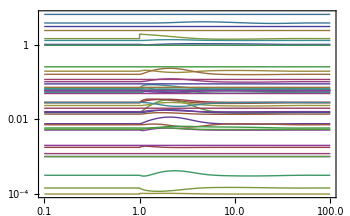

```mathematica
{concSol,fluxSol}=simulate[combiRelaxed2,{t,.1,100},Events->{"Glucose pulse"->WhenEvent[t==1,glu^c[t]->2Millimole Liter^-1]}];
plotSimulation[concSol]
```

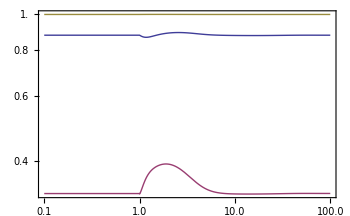

```mathematica
plotSimulation[{"E.C."->(adp^c/2+atp^c)/(adp^c+amp^c+atp^c),"Redox"->nadh^c/(nad^c+nadh^c),"Redox2"->nadph^c/(nadp^c+nadph^c)}/.concSol]
```

```mathematica
o2^Xt/.combiRelaxed2
```

0.0200788 Millimole Liter^-1

```mathematica
2.8684*10^-4
```

0.00028684

```mathematica
o2^Xt->(70+30 Cos[120 π t])2.8684*10^-4/.t->0
```

o2^Xt→0.028684

```mathematica
Solve[(70+30 Cos[120 π t])2.8684*10^-4==stripUnits[(o2^Xt/.combiRelaxed2)],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→-0.00416667},{t→0.00416667}}

```mathematica
{concSolHb,fluxSolHb}=simulate[combiRelaxed2,{t,0,.2},Parameters->{o2^Xt->(70+30 Cos[120 π t])2.8684*10^-4}];
```

```mathematica
o2Saturation={"r_OHb"->(25 (hbo2^c+2 hbo22^c+3 hbo23^c+4 hbo24^c))/(dhb^c+hb^c+hbo2^c+hbo22^c+hbo23^c+hbo24^c)};
```

```mathematica
plots={plotSimulation[o2Saturation/.concSolHb,PlotFunction->Plot,PlotRange->{All,{80,100}},FrameLabel->{"Time [h]","O_2 saturation [%]"}],plotSimulation[filter[fluxSolHb,{Subscript[v, vo2]}],PlotFunction->Plot,FrameLabel->{"Time [h]","Flux [mmol h^-1]"},Legend->{Bottom,Right}],plotSimulation[FilterRules[fluxSolHb,{Subscript[v, veno],Subscript[v, vpk],Subscript[v, vpglm]}],PlotFunction->Plot,Legend->True,FrameLabel->{"Time [h]","Flux [mmol h^-1]"}],
plotSimulation[FilterRules[fluxSolHb,{Subscript[v, vdpgm],Subscript[v, vdpgase]}],PlotFunction->Plot,Legend->True,FrameLabel->{"Time [h]","Flux [mmol h^-1]"}]};
```

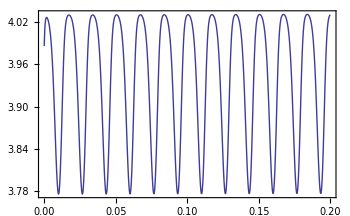

```mathematica
plotSimulation[FilterRules[concSolHb,{m["dpg23","c"]}],PlotFunction->Plot]
```

```mathematica
SlideView[plots]
```

```mathematica
glycolysis["Reactions"]
```

{(atp^c+glu^c⇌adp^c+g6p^c+h^c)^vhk,(g6p^c⇌f6p^c)^vpgi,(atp^c+f6p^c⇌adp^c+fdp^c+h^c)^vpfk,(dhap^c⇌gap^c)^vtpi,(fdp^c⇌dhap^c+gap^c)^vald,(gap^c+nad^c+phos^c⇌h^c+nadh^c+pg13^c)^vgapdh,(adp^c+pg13^c⇌atp^c+pg3^c)^vpgk,(pg3^c⇌pg2^c)^vpglm,(pg2^c⇌h2o^c+pep^c)^veno,(adp^c+h^c+pep^c⇌atp^c+pyr^c)^vpk,(h^c+nadh^c+pyr^c⇌lac^c+nad^c)^vldh,(amp^c⇌∅)^vamp,(2 adp^c⇌amp^c+atp^c)^vapk,(pyr^c⇌∅)^vpyr,(lac^c⇌∅)^vlac,(atp^c+h2o^c⇌adp^c+h^c+phos^c)^vatp,(nadh^c⇌h^c+nad^c)^vnadh,(∅⇌glu^c)^vgluin,(∅⇌amp^c)^vampin,(h^c⇌∅)^vh,(h2o^c⇌∅)^vh2o}

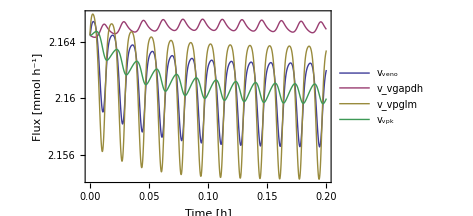

```mathematica
plotSimulation[FilterRules[fluxSolHb,{v["vgapdh"],Subscript[v, veno],Subscript[v, vpk],Subscript[v, vpglm]}],PlotFunction->LogPlot,Legend->True,FrameLabel->{"Time [h]","Flux [mmol h^-1]"}]
```

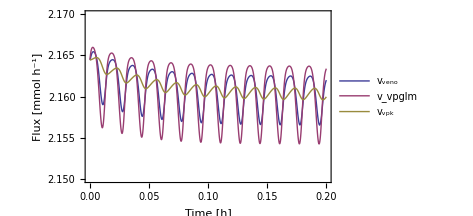

```mathematica
Show[plots[[3]],PlotRange->{All,{2.15,2.17}}]
```

```mathematica
FilterRules[fluxSolHb,{Subscript[v, veno],Subscript[v, vpk],Subscript[v, vpglm]}]
```

{v_veno→(1763.78 Liter Hour^-1) ((Millimole Liter^-1) InterpolatingFunction[{{0.,0.2}},<>][t]+(-0.59 Millimole Liter^-1) InterpolatingFunction[{{0.,0.2}},<>][t]),v_vpglm→(4869.57 Liter Hour^-1) ((-6.8 Millimole Liter^-1) InterpolatingFunction[{{0.,0.2}},<>][t]+(Millimole Liter^-1) InterpolatingFunction[{{0.,0.2}},<>][t]),v_vpk→(454.386 Liter^2 Hour^-1 Millimole^-1) ((Millimole^2 Liter^-2) InterpolatingFunction[{{0.,0.2}},<>][t] InterpolatingFunction[{{0.,0.2}},<>][t]+(-1/363000 Millimole^2 Liter^-2) InterpolatingFunction[{{0.,0.2}},<>][t] InterpolatingFunction[{{0.,0.2}},<>][t])}

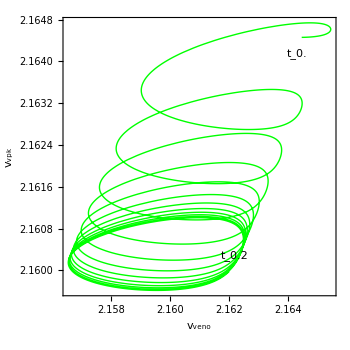

```mathematica
plotPhasePortrait[filter[fluxSolHb,{Subscript[v, veno],Subscript[v, vpk]}],PlotStyle->{Red,Green}]
plotPhasePortrait[filter[fluxSolHb,{Subscript[v, veno],Subscript[v, vpk]}],PlotStyle->{Red,Green}]
```

```mathematica
Show[plots[[3]],PlotRange->{All,{2.15,2.17}}]
```

-Graphics-

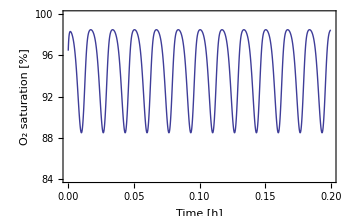

```mathematica
Show[plots[[1]],PlotRange->{All,{84,100}}]
```

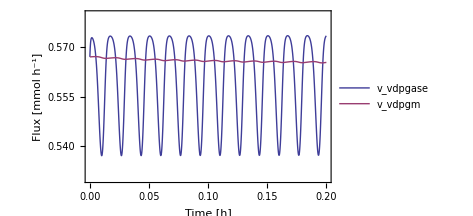

```mathematica
Show[plots[[4]],PlotRange->{All,{0.53,0.58}}]
```

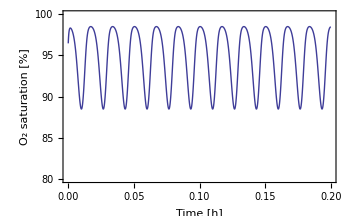

```mathematica
GraphicsGrid[{{plots[[1]],Show[plots[[3]],PlotRange->{All,{2.15,2.17}}]}}]
```

## Adding regulation

### Build and parameterize elementary reaction enzyme module for Phosphofruktokinase (PFK)

#### Construct the module

Write out the catalytic mechanism using textual input:

```mathematica
catalyticBranch={
"E_PFK[c]&atp + f6p[c] <=> E_PFK[c]&atp&f6p",
"E_PFK[c] + atp[c] <=> E_PFK[c]&atp",
"E_PFK[c]&atp&f6p -> E_PFK[c] + fdp[c] + adp[c] + h[c]"
};
```

Construct the enzyme module

```mathematica
module=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{amp^c},ActivationSites->4,Inhibitors->{atp^c},InhibitionSites->4];
```

The figure from the book is easier to grasp:

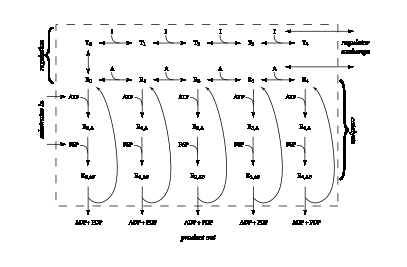

Don’t distinguish between the elementary rate-constants of the four different catalytic branches:

```mathematica
updateCustomRateLaws[module,Thread[(getID/@module["Fluxes"])->unifyRateConstants[module["Rates"]]]]
```

Include the inverses of the dissociation constants (from the book) as equilibrium constants in the model:

```mathematica
updateParameters[module,{Underscript[K, PFK1]->1/0.068,Underscript[K, PFK2]->1/0.1,Underscript[K, PFK_Activation_amp]->1/0.033,Underscript[K, PFK_Inhibition_atp]->1/0.1(*Increased by factor of 10*),Underscript[K, PFK_TransitionStep]->0.0011}]
```

#### Assumptions

The steady-state flux through the PFK sub network is given by

```mathematica
vpfkEq=p["v","pfk"]==rateconst["PFK3",True](Total[Cases[module["Species"],e_enzyme/;getCatalytic[e]==={m["atp","c"],m["f6p","c"]}]])
```

v_pfk==((PFK^c&atp^c&f6p^c)_^+(PFK^c&atp^c&f6p^c)_^(amp^c)+(PFK^c&atp^c&f6p^c)_^(amp^camp^c)+(PFK^c&atp^c&f6p^c)_^(amp^camp^camp^c)+(PFK^c&atp^c&f6p^c)_^(amp^camp^camp^camp^c)) k_PFK3^⟶

Enumerate all enzyme forms in the module:

```mathematica
enzForms=Cases[module["Species"],_enzyme]//Union
Length@enzForms
```

{(PFK^c)_^,(PFK^c)_^(amp^c),(PFK^c)_^(amp^camp^c),(PFK^c)_^(amp^camp^camp^c),(PFK^c)_^(amp^camp^camp^camp^c),(PFK^c&atp^c)_^,(PFK^c&atp^c)_^(amp^c),(PFK^c&atp^c)_^(amp^camp^c),(PFK^c&atp^c)_^(amp^camp^camp^c),(PFK^c&atp^c)_^(amp^camp^camp^camp^c),(PFK^c&atp^c&f6p^c)_^,(PFK^c&atp^c&f6p^c)_^(amp^c),(PFK^c&atp^c&f6p^c)_^(amp^camp^c),(PFK^c&atp^c&f6p^c)_^(amp^camp^camp^c),(PFK^c&atp^c&f6p^c)_^(amp^camp^camp^camp^c),(PFK_T^c)_^,(PFK_T^c)_(atp^c)^,(PFK_T^c)_(atp^catp^c)^,(PFK_T^c)_(atp^catp^catp^c)^,(PFK_T^c)_(atp^catp^catp^catp^c)^}

20

#### Solve the steady-state equations

Extract the ODE for the enzyme forms and set their time derivatives to zero to generate the steady-state equations:

```mathematica
enzPos=Flatten[Position[module["Species"],_enzyme]];
ssEq=stripTime[module["ODE"][[enzPos]]/._'[t]->0];
SlideView[ssEq]
```

Solve for the enzyme forms using the overall reaction and steady-state equations (anonymize speeds up the calculations by translating all enzyme, metabolite, constants etc. temporarily into anonymous variables); simplify the solution afterwards.

```mathematica
sol=anonymize[Solve[Join[ssEq,{vpfkEq}],enzForms]];
sol=Simplify[sol][[1]];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["PFK_ss_sol.m",sol];
sol=Import["PFK_ss_sol.m"];
```

```mathematica
SlideView[Simplify[keq2k@sol]]
```

#### The steady-state solution

In order to prepare Table 14.3 we need to obtain the four different 
categories of enzyme forms:

```mathematica
ri0=Cases[enzForms,e_enzyme/;getCatalytic[e]=={}&&getInhibitors[e]=={}&&getID[e]=="PFK"];
riA=Cases[enzForms,e_enzyme/;getCatalytic[e]=={atp^c}&&getInhibitors[e]=={}&&getID[e]=="PFK"];
riAF=Cases[enzForms,e_enzyme/;getCatalytic[e]=={atp^c,f6p^c}&&getInhibitors[e]=={}&&getID[e]=="PFK"];
tforms=Cases[enzForms,e_enzyme/;getID[e]=="PFK_T"];
```

```mathematica
SlideView[{ri0,riA,riAF,tforms}]
```

Now we can generate Table 14.3:

```mathematica
tab14$3=Simplify@Grid[Join[{{"i","R_(i, 0)","R_(i, 0)/R_(i, 0)","R_(i, A)/R_(i, 0)","R_(i, AF)/R_(i, 0)","R_(i, 0)/R_(1, 0)","T_i/T_0"}},Transpose[{{0,1,2,3,4},
ri0,
ri0/ri0,
ri0/riA,
ri0/riAF,
ri0/ri0[[1]],
tforms/tforms[[1]]
}/.keq2k@sol]],Dividers->{{False,True},{False,True}}]
```

i | R_(i, 0) | R_(i, 0)/R_(i, 0) | R_(i, A)/R_(i, 0) | R_(i, AF)/R_(i, 0) | R_(i, 0)/R_(1, 0) | T_i/T_0
0 | (v_pfk (f6p^c k_PFK2^⟶ k_PFK3^⟶+k_PFK1^⟵ (k_PFK2^⟵+k_PFK3^⟶)) (k_PFK_Activation_amp^⟵)^4)/(atp^c f6p^c k_PFK1^⟶ k_PFK2^⟶ k_PFK3^⟶ (k_PFK_Activation_amp^⟵+amp^c k_PFK_Activation_amp^⟶)^4) | 1 | (f6p^c k_PFK2^⟶ k_PFK3^⟶+k_PFK1^⟵ (k_PFK2^⟵+k_PFK3^⟶))/(atp^c k_PFK1^⟶ (k_PFK2^⟵+k_PFK3^⟶)) | (f6p^c k_PFK2^⟶ k_PFK3^⟶+k_PFK1^⟵ (k_PFK2^⟵+k_PFK3^⟶))/(atp^c f6p^c k_PFK1^⟶ k_PFK2^⟶) | 1 | 1
1 | (4 amp^c v_pfk (f6p^c k_PFK2^⟶ k_PFK3^⟶+k_PFK1^⟵ (k_PFK2^⟵+k_PFK3^⟶)) (k_PFK_Activation_amp^⟵)^3 k_PFK_Activation_amp^⟶)/(atp^c f6p^c k_PFK1^⟶ k_PFK2^⟶ k_PFK3^⟶ (k_PFK_Activation_amp^⟵+amp^c k_PFK_Activation_amp^⟶)^4) | 1 | (f6p^c k_PFK2^⟶ k_PFK3^⟶+k_PFK1^⟵ (k_PFK2^⟵+k_PFK3^⟶))/(atp^c k_PFK1^⟶ (k_PFK2^⟵+k_PFK3^⟶)) | (f6p^c k_PFK2^⟶ k_PFK3^⟶+k_PFK1^⟵ (k_PFK2^⟵+k_PFK3^⟶))/(atp^c f6p^c k_PFK1^⟶ k_PFK2^⟶) | (4 amp^c k_PFK_Activation_amp^⟶)/k_PFK_Activation_amp^⟵ | (4 atp^c k_PFK_Inhibition_atp^⟶)/k_PFK_Inhibition_atp^⟵
2 | (6 (amp^c)^2 v_pfk (f6p^c k_PFK2^⟶ k_PFK3^⟶+k_PFK1^⟵ (k_PFK2^⟵+k_PFK3^⟶)) (k_PFK_Activation_amp^⟵)^2 (k_PFK_Activation_amp^⟶)^2)/(atp^c f6p^c k_PFK1^⟶ k_PFK2^⟶ k_PFK3^⟶ (k_PFK_Activation_amp^⟵+amp^c k_PFK_Activation_amp^⟶)^4) | 1 | (f6p^c k_PFK2^⟶ k_PFK3^⟶+k_PFK1^⟵ (k_PFK2^⟵+k_PFK3^⟶))/(atp^c k_PFK1^⟶ (k_PFK2^⟵+k_PFK3^⟶)) | (f6p^c k_PFK2^⟶ k_PFK3^⟶+k_PFK1^⟵ (k_PFK2^⟵+k_PFK3^⟶))/(atp^c f6p^c k_PFK1^⟶ k_PFK2^⟶) | (6 (amp^c)^2 (k_PFK_Activation_amp^⟶)^2)/((k_PFK_Activation_amp^⟵)^2) | (6 (atp^c)^2 (k_PFK_Inhibition_atp^⟶)^2)/((k_PFK_Inhibition_atp^⟵)^2)
3 | (4 (amp^c)^3 v_pfk (f6p^c k_PFK2^⟶ k_PFK3^⟶+k_PFK1^⟵ (k_PFK2^⟵+k_PFK3^⟶)) k_PFK_Activation_amp^⟵ (k_PFK_Activation_amp^⟶)^3)/(atp^c f6p^c k_PFK1^⟶ k_PFK2^⟶ k_PFK3^⟶ (k_PFK_Activation_amp^⟵+amp^c k_PFK_Activation_amp^⟶)^4) | 1 | (f6p^c k_PFK2^⟶ k_PFK3^⟶+k_PFK1^⟵ (k_PFK2^⟵+k_PFK3^⟶))/(atp^c k_PFK1^⟶ (k_PFK2^⟵+k_PFK3^⟶)) | (f6p^c k_PFK2^⟶ k_PFK3^⟶+k_PFK1^⟵ (k_PFK2^⟵+k_PFK3^⟶))/(atp^c f6p^c k_PFK1^⟶ k_PFK2^⟶) | (4 (amp^c)^3 (k_PFK_Activation_amp^⟶)^3)/((k_PFK_Activation_amp^⟵)^3) | (4 (atp^c)^3 (k_PFK_Inhibition_atp^⟶)^3)/((k_PFK_Inhibition_atp^⟵)^3)
4 | ((amp^c)^4 v_pfk (f6p^c k_PFK2^⟶ k_PFK3^⟶+k_PFK1^⟵ (k_PFK2^⟵+k_PFK3^⟶)) (k_PFK_Activation_amp^⟶)^4)/(atp^c f6p^c k_PFK1^⟶ k_PFK2^⟶ k_PFK3^⟶ (k_PFK_Activation_amp^⟵+amp^c k_PFK_Activation_amp^⟶)^4) | 1 | (f6p^c k_PFK2^⟶ k_PFK3^⟶+k_PFK1^⟵ (k_PFK2^⟵+k_PFK3^⟶))/(atp^c k_PFK1^⟶ (k_PFK2^⟵+k_PFK3^⟶)) | (f6p^c k_PFK2^⟶ k_PFK3^⟶+k_PFK1^⟵ (k_PFK2^⟵+k_PFK3^⟶))/(atp^c f6p^c k_PFK1^⟶ k_PFK2^⟶) | ((amp^c)^4 (k_PFK_Activation_amp^⟶)^4)/((k_PFK_Activation_amp^⟵)^4) | ((atp^c)^4 (k_PFK_Inhibition_atp^⟶)^4)/((k_PFK_Inhibition_atp^⟵)^4)

Make it look similar to the table in the book:

```mathematica
tab14$3/.{Subscript[k, PFK3]^⟶->Subscript[k, PFK]^⟶,Subscript[k, PFK1]^⟶->Subscript[k, A]^⟶,Subscript[k, PFK1]^⟵->Subscript[k, A]^⟵,Subscript[k, PFK2]^⟶->Subscript[k, F]^⟶,Subscript[k, PFK2]^⟵->Subscript[k, F]^⟵,Subscript[k, PFK_Activation_amp]^⟶->Subscript[k, a]^⟶,Subscript[k, PFK_Activation_amp]^⟵->Subscript[k, a]^⟵,Subscript[k, PFK_Inhibition_atp]^⟶->Subscript[k, i]^⟶,Subscript[k, PFK_Inhibition_atp]^⟵->Subscript[k, i]^⟵}
```

i | R_(i, 0) | R_(i, 0)/R_(i, 0) | R_(i, A)/R_(i, 0) | R_(i, AF)/R_(i, 0) | R_(i, 0)/R_(1, 0) | T_i/T_0
0 | (v_pfk (k_a^⟵)^4 (f6p^c k_F^⟶ k_PFK^⟶+k_A^⟵ (k_F^⟵+k_PFK^⟶)))/(atp^c f6p^c (k_a^⟵+amp^c k_a^⟶)^4 k_A^⟶ k_F^⟶ k_PFK^⟶) | 1 | (f6p^c k_F^⟶ k_PFK^⟶+k_A^⟵ (k_F^⟵+k_PFK^⟶))/(atp^c k_A^⟶ (k_F^⟵+k_PFK^⟶)) | (f6p^c k_F^⟶ k_PFK^⟶+k_A^⟵ (k_F^⟵+k_PFK^⟶))/(atp^c f6p^c k_A^⟶ k_F^⟶) | 1 | 1
1 | (4 amp^c v_pfk (k_a^⟵)^3 k_a^⟶ (f6p^c k_F^⟶ k_PFK^⟶+k_A^⟵ (k_F^⟵+k_PFK^⟶)))/(atp^c f6p^c (k_a^⟵+amp^c k_a^⟶)^4 k_A^⟶ k_F^⟶ k_PFK^⟶) | 1 | (f6p^c k_F^⟶ k_PFK^⟶+k_A^⟵ (k_F^⟵+k_PFK^⟶))/(atp^c k_A^⟶ (k_F^⟵+k_PFK^⟶)) | (f6p^c k_F^⟶ k_PFK^⟶+k_A^⟵ (k_F^⟵+k_PFK^⟶))/(atp^c f6p^c k_A^⟶ k_F^⟶) | (4 amp^c k_a^⟶)/k_a^⟵ | (4 atp^c k_i^⟶)/k_i^⟵
2 | (6 (amp^c)^2 v_pfk (k_a^⟵)^2 (k_a^⟶)^2 (f6p^c k_F^⟶ k_PFK^⟶+k_A^⟵ (k_F^⟵+k_PFK^⟶)))/(atp^c f6p^c (k_a^⟵+amp^c k_a^⟶)^4 k_A^⟶ k_F^⟶ k_PFK^⟶) | 1 | (f6p^c k_F^⟶ k_PFK^⟶+k_A^⟵ (k_F^⟵+k_PFK^⟶))/(atp^c k_A^⟶ (k_F^⟵+k_PFK^⟶)) | (f6p^c k_F^⟶ k_PFK^⟶+k_A^⟵ (k_F^⟵+k_PFK^⟶))/(atp^c f6p^c k_A^⟶ k_F^⟶) | (6 (amp^c)^2 (k_a^⟶)^2)/((k_a^⟵)^2) | (6 (atp^c)^2 (k_i^⟶)^2)/((k_i^⟵)^2)
3 | (4 (amp^c)^3 v_pfk k_a^⟵ (k_a^⟶)^3 (f6p^c k_F^⟶ k_PFK^⟶+k_A^⟵ (k_F^⟵+k_PFK^⟶)))/(atp^c f6p^c (k_a^⟵+amp^c k_a^⟶)^4 k_A^⟶ k_F^⟶ k_PFK^⟶) | 1 | (f6p^c k_F^⟶ k_PFK^⟶+k_A^⟵ (k_F^⟵+k_PFK^⟶))/(atp^c k_A^⟶ (k_F^⟵+k_PFK^⟶)) | (f6p^c k_F^⟶ k_PFK^⟶+k_A^⟵ (k_F^⟵+k_PFK^⟶))/(atp^c f6p^c k_A^⟶ k_F^⟶) | (4 (amp^c)^3 (k_a^⟶)^3)/((k_a^⟵)^3) | (4 (atp^c)^3 (k_i^⟶)^3)/((k_i^⟵)^3)
4 | ((amp^c)^4 v_pfk (k_a^⟶)^4 (f6p^c k_F^⟶ k_PFK^⟶+k_A^⟵ (k_F^⟵+k_PFK^⟶)))/(atp^c f6p^c (k_a^⟵+amp^c k_a^⟶)^4 k_A^⟶ k_F^⟶ k_PFK^⟶) | 1 | (f6p^c k_F^⟶ k_PFK^⟶+k_A^⟵ (k_F^⟵+k_PFK^⟶))/(atp^c k_A^⟶ (k_F^⟵+k_PFK^⟶)) | (f6p^c k_F^⟶ k_PFK^⟶+k_A^⟵ (k_F^⟵+k_PFK^⟶))/(atp^c f6p^c k_A^⟶ k_F^⟶) | ((amp^c)^4 (k_a^⟶)^4)/((k_a^⟵)^4) | ((atp^c)^4 (k_i^⟶)^4)/((k_i^⟵)^4)

#### Numerical values

The conserved enzyme pool

```mathematica
pfktot=p["PFKtot"]==Total[enzForms]
```

PFKtot_Global==(PFK^c)_^+(PFK^c)_^(amp^c)+(PFK^c)_^(amp^camp^c)+(PFK^c)_^(amp^camp^camp^c)+(PFK^c)_^(amp^camp^camp^camp^c)+(PFK^c&atp^c)_^+(PFK^c&atp^c)_^(amp^c)+(PFK^c&atp^c)_^(amp^camp^c)+(PFK^c&atp^c)_^(amp^camp^camp^c)+(PFK^c&atp^c)_^(amp^camp^camp^camp^c)+(PFK^c&atp^c&f6p^c)_^+(PFK^c&atp^c&f6p^c)_^(amp^c)+(PFK^c&atp^c&f6p^c)_^(amp^camp^c)+(PFK^c&atp^c&f6p^c)_^(amp^camp^camp^c)+(PFK^c&atp^c&f6p^c)_^(amp^camp^camp^camp^c)+(PFK_T^c)_^+(PFK_T^c)_(atp^c)^+(PFK_T^c)_(atp^catp^c)^+(PFK_T^c)_(atp^catp^catp^c)^+(PFK_T^c)_(atp^catp^catp^catp^c)^

Substitute all know parameters and the steady-state solutions

```mathematica
pfktot=Simplify[pfktot/.sol/.stripUnits@combiRelaxed["InitialConditions"]/.Underscript[v, pfk]->1.12/.module["Parameters"]]
```

PFKtot_Global==1.07116/k_PFK1^⟶+60.2444/k_PFK2^⟶+7.14444/k_PFK3^⟶

Solver for k_PFK3^⟶

```mathematica
kpfkSol=Quiet[Solve[pfktot,Subscript[k, PFK3]^⟶][[1]],Solve::ratnz]
```

{k_PFK3^⟶→(8.64348×10^14 k_PFK1^⟶ k_PFK2^⟶)/(-7.28848×10^15 k_PFK1^⟶-1.29591×10^14 k_PFK2^⟶+1.20982×10^14 PFKtot_Global k_PFK1^⟶ k_PFK2^⟶)}

Plot the feasible parameters space and color code the fraction of T-form enzymes

```mathematica
tFraction=Simplify[Total[tforms]/Total[enzForms]/.sol]/.module["Parameters"]/.stripUnits[glycolysis["InitialConditions"]];
tFractionFunction=tFraction/.{Subscript[k, PFK1]^⟶->#1,Subscript[k, PFK2]^⟶->#2,Subscript[k, PFK3]^⟶->#3}&;
tFractionFunctionLog=tFraction/.{Subscript[k, PFK1]^⟶->10^#1,Subscript[k, PFK2]^⟶->10^#2,Subscript[k, PFK3]^⟶->10^#3}&;
tFractionColorFunction=ColorData["DarkBand"][tFraction/.{Subscript[k, PFK1]^⟶->#1,Subscript[k, PFK2]^⟶->#2,Subscript[k, PFK3]^⟶->#3}]&;
tFractionColorFunctionLog=ColorData["DarkBands"][tFraction/.{Subscript[k, PFK1]^⟶->10^#1,Subscript[k, PFK2]^⟶->10^#2,Subscript[k, PFK3]^⟶->10^#3}]&;
paramSpacePlot=Legended[Plot3D[Evaluate[Log[10,Subscript[k, PFK3]^⟶/.kpfkSol/.{Subscript[k, PFK1]^⟶->10^kap,Subscript[k, PFK2]^⟶->10^kfp,Underscript[PFKtot, Global]->33*^-6}]],{kap,1,10},{kfp,1,10},ColorFunction->tFractionColorFunctionLog,ColorFunctionScaling->False,PlotPoints->100,PlotRange->{Full,Full,{5,9}},AxesLabel->{"k_A^+ [log_10]","k_F^+ [log_10]","k_PFK^+ [log_10]"},ImageSize->500,ViewPoint->{Pi,Pi/2,2}],BarLegend[{"DarkBands",{0,1}},LegendLayout->"Column",LegendLabel->"T/PFK_tot",LabelStyle->{FontFamily->"Helvetica"}]]
AutoCollapse[]
```

-Graphics3D-

The enzyme is inhibited between 10–15% under physiological conditions (Ponce et al. Biochimica et Biophysica Acta 1971 250(1):63-74). The parameter values indicated in green correspond to a 10–15% fraction of T-forms.

```mathematica
stripePlot=Legended[Plot3D[Evaluate[Log[10,Subscript[k, PFK3]^⟶/.kpfkSol/.{Subscript[k, PFK1]^⟶->10^kap,Subscript[k, PFK2]^⟶->10^kfp,Underscript[PFKtot, Global]->33*^-6}]],{kap,0,12},{kfp,0,12},ColorFunction->(If[.1<tFractionFunctionLog[##]<.15,Green,LightGray]&),ColorFunctionScaling->False,AxesLabel->{"k_A^+ [log_10]","k_F^+ [log_10]","k_PFK^+ [log_10]"},PlotPoints->100,PlotRange->{Full,Full,{5,9}},ImageSize->500,ViewPoint->{Pi,Pi/2,2}],SwatchLegend[{Green},{"10–15% T-fraction"}]]
AutoCollapse[]
```

-Graphics3D-

Choose a feasible parameter combination

```mathematica
finalParamChoice={Subscript[k, PFK1]^⟶->116686.,Subscript[k, PFK2]^⟶->8.259528*^6,Subscript[k, PFK3]^⟶->432308.4041452617};
```

```mathematica
Show[stripePlot,Graphics3D[{PointSize[.05],Red,Point[#]}&@(Log[10,finalParamChoice/.r_Rule:>r[[2]]])],PlotRange->All]
AutoCollapse[]
```

-Graphics3D-

```mathematica
Show[paramSpacePlot,Graphics3D[{PointSize[.05],Red,Point[#]}&@(Log[10,finalParamChoice/.r_Rule:>r[[2]]])],PlotRange->All]
```

-Graphics3D-

Parameterize the final PFK module and make it ready for integration

```mathematica
finalPFK=module;
updateParameters[finalPFK,finalParamChoice]
(*Add fast activation and inhibition rate-constants*)
updateParameters[finalPFK,{Subscript[k, PFK_Activation_amp]^⟶->1000000,Subscript[k, PFK_Inhibition_atp]^⟶->1000000,Subscript[k, PFK_TransitionStep]^⟶->1000000^2}]
(*updateParameters[finalPFK,{Subscript[k, PFK_Activation_amp]^⟶->10000,Subscript[k, PFK_Inhibition_atp]^⟶->10000,Subscript[k, PFK_TransitionStep]^⟶->10000^2}]*)
```

Calculate the numerical steady-state concentrations for the different enzyme forms:

```mathematica
enzFormConc=sol/.{parameter["v","pfk"]->1.12}/.stripUnits[finalPFK["Parameters"]]/.stripUnits[combiRelaxed["InitialConditions"]]
Total[enzFormConc[[All,2]]]
```

{(PFK^c)_^→3.9511×10^-8,(PFK^c)_^(amp^c)→4.1536×10^-7,(PFK^c)_^(amp^camp^c)→1.63743×10^-6,(PFK^c)_^(amp^camp^camp^c)→2.86891×10^-6,(PFK^c)_^(amp^camp^camp^camp^c)→1.88496×10^-6,(PFK^c&atp^c)_^→1.15039×10^-7,(PFK^c&atp^c)_^(amp^c)→1.20935×10^-6,(PFK^c&atp^c)_^(amp^camp^c)→4.76748×10^-6,(PFK^c&atp^c)_^(amp^camp^camp^c)→8.35303×10^-6,(PFK^c&atp^c)_^(amp^camp^camp^camp^c)→5.4882×10^-6,(PFK^c&atp^c&f6p^c)_^→1.49519×10^-8,(PFK^c&atp^c&f6p^c)_^(amp^c)→1.57181×10^-7,(PFK^c&atp^c&f6p^c)_^(amp^camp^c)→6.19639×10^-7,(PFK^c&atp^c&f6p^c)_^(amp^camp^camp^c)→1.08566×10^-6,(PFK^c&atp^c&f6p^c)_^(amp^camp^camp^camp^c)→7.13312×10^-7,(PFK_T^c)_^→4.34621×10^-11,(PFK_T^c)_(atp^c)^→2.78158×10^-9,(PFK_T^c)_(atp^catp^c)^→6.67578×10^-8,(PFK_T^c)_(atp^catp^catp^c)^→7.12083×10^-7,(PFK_T^c)_(atp^catp^catp^catp^c)^→2.84833×10^-6}

0.000033

Include the enzyme concentrations in the inital conditions of the module

```mathematica
updateInitialConditions[finalPFK,enzFormConc]
```

### Integrate the PFK module into the RBC model

Integrate the parametrized PFK module with the glycolytic pathway.

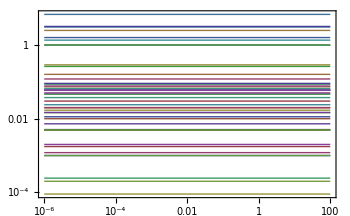

```mathematica
plotSimulation@simulate[combiRelaxed,{t,0,100}][[1]]
```

```mathematica
combiPFK=Union[deleteReactions[combiRelaxed,{"vpfk"}],finalPFK];
```

The system is initially in a steady-state.

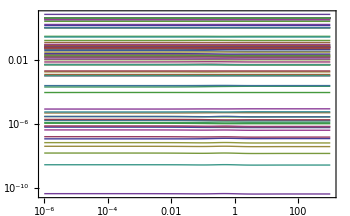

```mathematica
{concSol,fluxSol}=simulate[combiPFK,{t,0,1000}];
plotSimulation[concSol]
```

```mathematica
{concSolHb,fluxSolHb}=simulate[combiPFK,{t,0,5},Parameters->{o2^Xt->(70+30 Cos[120 π t])2.8684*10^-4},Events->{"pulse"->WhenEvent[t==.1,glu^c[t]->2]},MaxSteps->∞];
```

```mathematica
SlideView[{plotSimulation[o2Saturation/.concSolHb,PlotFunction->Plot,PlotRange->{All,{80,100}},FrameLabel->{"Time [h]","O_2 saturation [%]"},Tooltipped->False],plotSimulation[filter[fluxSolHb,{Subscript[v, vo2]}],PlotFunction->Plot,FrameLabel->{"Time [h]","Flux [mmol h^-1]"},Legend->{Bottom,Right},Tooltipped->False],plotSimulation[FilterRules[fluxSolHb,{Subscript[v, veno],Subscript[v, vpk],Subscript[v, vpglm]}],PlotFunction->Plot,Legend->True,FrameLabel->{"Time [h]","Flux [mmol h^-1]"},Tooltipped->False],
plotSimulation[FilterRules[fluxSolHb,{Subscript[v, vdpgm],Subscript[v, vdpgase]}],PlotFunction->Plot,Legend->True,FrameLabel->{"Time [h]","Flux [mmol h^-1]"},Tooltipped->False]}]
```

Compare the dynamic responses of glycolysis with and without the PFK sub-network to a 50% increase in ATP usage.

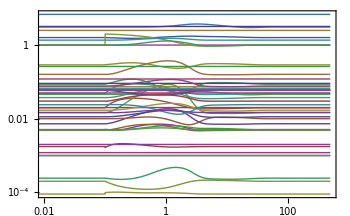

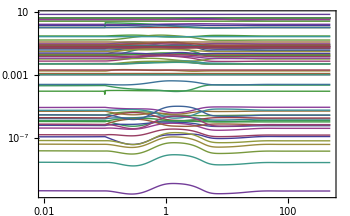

```mathematica
{perturbedConcSol1,perturbedFluxSol1}=simulate[combiRelaxed,{t,0,500},Events->{"pulse"->WhenEvent[t==.1,glu^c[t]->2.]}];
plotSimulation[perturbedConcSol1,PlotRange->{{0.01,All},All}]
{perturbedConcSol2,perturbedFluxSol2}=simulate[combiPFK,{t,0,500},Events->{"pulse"->WhenEvent[t==.1,glu^c[t]->2.]}];
plotSimulation[perturbedConcSol2,PlotRange->{{0.01,All},All}]
```

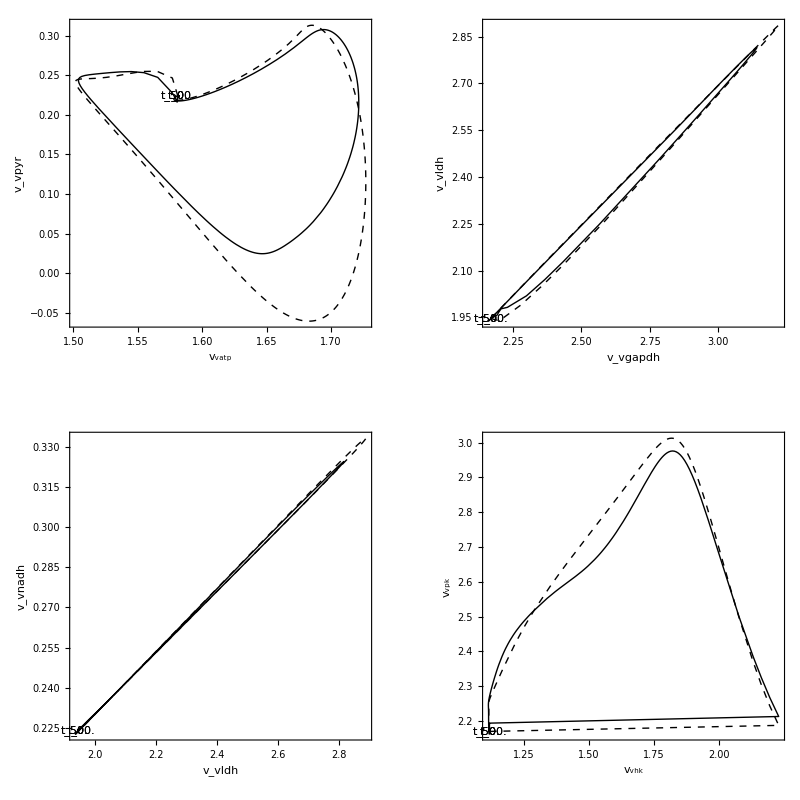

```mathematica
pairwisePlots=Table[
filteredSol={filter[perturbedFluxSol1,cmb],filter[perturbedFluxSol2,cmb]};
plotPhasePortrait[filteredSol,PlotStyle->{Directive[Black,Dashed],Directive[Black]},PlotPoints->500,FrameLabel->filteredSol[[1,All,1]]],{cmb,{{Subscript[v, vatp],Subscript[v, vpyr]},{Subscript[v, vgapdh],Subscript[v, vldh]},{Subscript[v, vldh],Subscript[v, vnadh]},{Subscript[v, vhk],Subscript[v, vpk]}}}];
Legended[GraphicsGrid[Partition[pairwisePlots,2],ImageSize->800],LineLegend[{Black,Directive[Black,Dashed]},{"Regulated","Unregulated"}]]
```

```mathematica
ratios={"Redox"->nadh^c/(nad^c+nadh^c),"E.C."->(adp^c/2+atp^c)/(adp^c+amp^c+atp^c),"T_fraction"->Total[tforms]/Total[enzForms]};
```

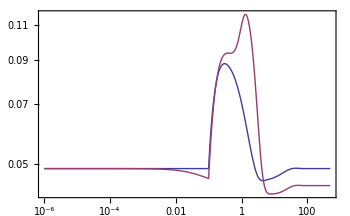

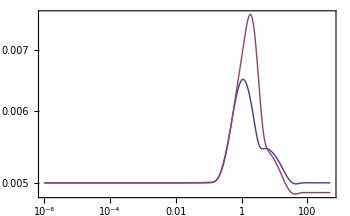

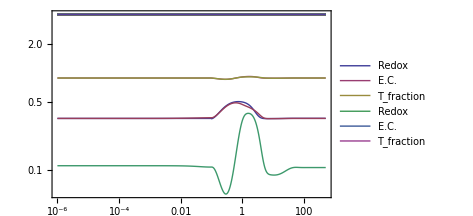

-Graphics-

```mathematica
plotSimulation[Join[filter[perturbedConcSol1,{m["g6p","c"]}],filter[perturbedConcSol2,{m["g6p","c"]}]]]
plotSimulation[Join[filter[perturbedConcSol1,{m["prpp","c"]}],filter[perturbedConcSol2,{m["prpp","c"]}]]]
plotSimulation[Join[ratios/.perturbedConcSol1,ratios/.perturbedConcSol2],Legend->True]
plotSimulation[Join[ratios/.perturbedConcSol1,ratios/.perturbedConcSol2],Legend->True]
```

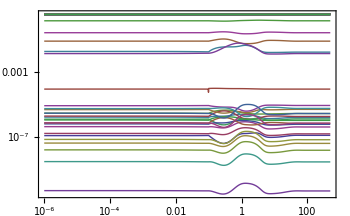

```mathematica
plotSimulation[FilterRules[perturbedConcSol2,finalPFK["Species"]]]
```

```mathematica
scatterConc=scatterFromDicts[stripUnits[perturbedConcSol1],stripUnits[perturbedConcSol2]];
```

```mathematica
SlideView[ListPlot[#[[2]],PlotLabel->#[[1]],Joined->True,PlotMarkers->Automatic]&/@(#[[1]]->Thread[#[[2]]/.t->10^Range[-4,3,.1]]&/@scatterConc)]
```

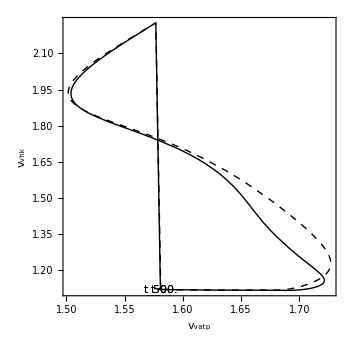

```mathematica
filteredSol=stripUnits@{filter[perturbedFluxSol1,{Subscript[v, vatp],v["vhk"]}],filter[perturbedFluxSol2,{Subscript[v, vatp],v["vhk"]}]};
plotPhasePortrait[filteredSol,PlotStyle->{Directive[Black,Dashed],Directive[Black]},PlotPoints->500,FrameLabel->filteredSol[[1,All,1]]]
```

```mathematica
keyRatios={"r_R"->Total[Cases[combiPFK["Species"],e_enzyme/;getID[e]≠"PFK_T"]]/Total[Cases[combiPFK["Species"],e_enzyme]],
"E.C."->(adp^c/2+atp^c)/(adp^c+amp^c+atp^c)
};
```

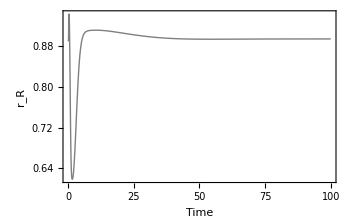

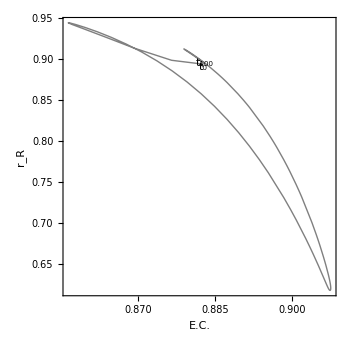

```mathematica
plotSimulation[filter[keyRatios,{"r_R"}]/.perturbedConcSol2,{t,0,100},PlotFunction->Plot,FrameLabel->{"Time","r_R"},PlotStyle->Gray]
plotPhasePortrait[filter[keyRatios,{"E.C.","r_R"}]/.perturbedConcSol2,{t,0,100},PlotStyle->Gray]
```

```mathematica
Module[{concSol},
Manipulate[
concSol=simulate[combiPFK,{t,0,100},Events->{"pulse"->WhenEvent[t==.1,glu^c[t]->glu]},Method->Automatic,PrecisionGoal->23][[1]];
GraphicsRow[{plotSimulation[filter[keyRatios,{"r_R"}]/.concSol,{t,0,100},PlotFunction->Plot,FrameLabel->{"Time","r_R"},Tooltipped->False,PlotRange->{All,{0.5,1.1}},PlotStyle->Black],
plotPhasePortrait[filter[keyRatios,{"E.C.","r_R"}]/.concSol,{t,0,100},PlotStyle->Gray,PlotRange->{{0.8,1},{0.65,1}}]}],{{glu,1,"Glucose conc."},.1,2}]]
(*AutoCollapse[]*)
```

```mathematica
combi//Dimensions
```

{48,53}

```mathematica
combiPFK//Dimensions
```

{68,76}

## Sensitivity analysis

```mathematica
Needs["HierarchicalClustering`"]
```

```mathematica
glycolysis=ExampleData[{"Toolbox","Glycolysis"}];
setUnitChecking[glycolysis,False]
```

```mathematica
initialConcOfInterest=stripUnits[FilterRules[glycolysis["InitialConditions"],_metabolite]][[1;;5]]
```

{glu^c→1.,g6p^c→0.0486,f6p^c→0.0198,fdp^c→0.0146,dhap^c→0.16}

```mathematica
(*{output,freq,divisions}=FASTsimul[(findSteadyState[glycolysis,InitialConditions->#,"Strategy"->simulate,Method->"BDF"][[1]])[[All,2]]&,initialConcOfInterest];*)
{output,freq,divisions}=FASTsimul[(simulate[glycolysis,{t,0,1*^6},InitialConditions->#,Method->"BDF"][[1]]/.t->1*^6)[[All,2]]&,RandomSample@initialConcOfInterest];
```

```mathematica
sensitivities=FASTcalcSensitivities[output,freq,divisions];
```

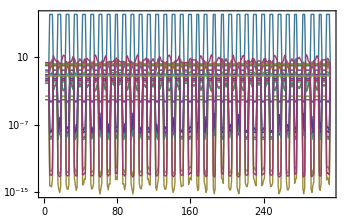

```mathematica
ListLogPlot[Transpose[output],Joined->True]
```

```mathematica
sensitivities[[All,2]]//Dimensions
```

{5,20}

```mathematica
sensitivities
```

{fdp^c→{0.00524084,6.29456×10^-15,0.028915,0.028787,0.0055938,0.153674,0.013649,0.0016113,-20240.4,4.85635×10^-7,-3.62623×10^-17,0.00650708,-0.000543046,0.000543046,0.000307214,4.39146×10^-6,0.000204208,0.00139692,0.388275,5.43046×10^-6},f6p^c→{-0.0067733,7.82023×10^-15,-0.0373699,0.0795477,0.014601,0.15743,0.035605,0.00458909,26158.9,-6.27638×10^-7,-1.08792×10^-17,-0.0084098,0.000701837,-0.000701837,-0.000397064,-5.67556×10^-6,-0.00026393,-0.00180547,0.184205,-7.01837×10^-6},dhap^c→{0.00677528,2.93618×10^-14,0.0373808,0.163355,0.0371164,0.621553,0.090535,0.00929106,-26166.6,6.27821×10^-7,1.26468×10^-18,0.00841226,-0.000702042,0.000702042,0.000397154,5.67721×10^-6,0.000263992,0.00180589,2.81231,7.02042×10^-6},glu^c→{-0.178535,8.12562×10^-14,-0.985019,1.10131,0.469997,1.68834,1.14614,0.0640786,689537.,-0.0000165437,1.14018×10^-18,-0.221671,0.0184994,-0.0184994,-0.0104658,-0.0001496,-0.00695668,-0.0475886,-3.94432,-0.000184994},g6p^c→{-0.00817969,1.49686×10^-14,-0.0451293,0.118951,0.0367368,0.281138,0.0895933,0.00684976,31590.7,-7.5796×10^-7,-6.95583×10^-19,-0.010156,0.000847565,-0.000847565,-0.000479505,-6.85402×10^-6,-0.000318729,-0.00218033,0.644559,-8.47565×10^-6}}

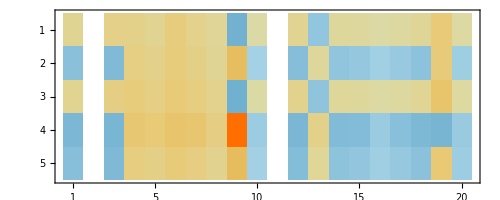

```mathematica
MatrixPlot[sensitivities[[All,2]]]
```

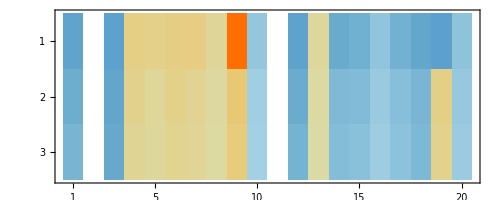

```mathematica
MatrixPlot[sensitivities[[All,2]]]
```

```mathematica
#[[1]]->SortBy[Thread[glycolysis["Species"]->#[[2]]],-Abs[#[[2]]]&]&/@sensitivities
```

{glu^c→{glu^c→15.2504,nadh^c→-13.6014,fdp^c→5.09317,dhap^c→1.17497,g6p^c→0.883136,pyr^c→0.419518,f6p^c→0.362104,pg2^c→0.259431,adp^c→-0.183804,amp^c→-0.111186,pg13^c→0.104753,gap^c→0.0672975,pg3^c→0.0616995,lac^c→-0.031574,atp^c→0.00325957,nad^c→0.00285235,pep^c→-0.00285235,phos^c→3.38078×10^-6,h2o^c→-1.89844×10^-6,h^c→-1.70113×10^-6},g6p^c→{fdp^c→0.3473,nadh^c→0.256787,glu^c→0.139273,dhap^c→0.107374,g6p^c→0.0788856,pyr^c→0.0666389,amp^c→0.0507943,f6p^c→0.0323432,pg2^c→0.030755,pg13^c→0.0166149,adp^c→0.0127758,pg3^c→0.0098,gap^c→0.00614349,atp^c→0.0046283,lac^c→-0.00164188,nad^c→0.000132369,pep^c→-0.000132369,phos^c→6.02214×10^-6,h2o^c→-1.13993×10^-7,h^c→6.60551×10^-8},f6p^c→{fdp^c→0.241531,dhap^c→0.0675608,nadh^c→-0.0530685,glu^c→0.0385083,g6p^c→0.031544,pyr^c→0.0222097,f6p^c→0.0129337,atp^c→-0.00792974,pg2^c→-0.00792396,amp^c→0.00667105,adp^c→0.00589482,pg13^c→0.00554647,gap^c→0.00386927,pg3^c→0.00326646,lac^c→-0.00202896,nad^c→0.000159911,pep^c→-0.000159911,phos^c→-3.5965×10^-7,h^c→-1.53369×10^-7,h2o^c→5.81053×10^-9},fdp^c→{fdp^c→0.244709,glu^c→-0.171463,dhap^c→0.0804948,nadh^c→0.0518263,pyr^c→0.0516386,atp^c→0.0322053,pg2^c→0.0250642,pg13^c→0.01285,pg3^c→0.00759331,adp^c→-0.00508153,gap^c→0.00458873,amp^c→-0.00443243,g6p^c→0.00346341,lac^c→0.00218067,f6p^c→0.0014202,nad^c→-0.00011353,pep^c→0.00011353,phos^c→0.0000185728,h2o^c→-2.42792×10^-7,h^c→2.04008×10^-7},dhap^c→{nadh^c→1.69209,fdp^c→0.995997,dhap^c→0.304865,pyr^c→0.127133,amp^c→0.100775,glu^c→-0.0686666,pg2^c→0.0581484,atp^c→0.0394162,g6p^c→0.0336036,pg13^c→0.0316786,adp^c→0.0270491,pg3^c→0.0186958,gap^c→0.0174181,f6p^c→0.0137776,lac^c→0.000575237,phos^c→0.000014616,pep^c→-0.0000106343,nad^c→0.0000106343,h2o^c→-4.5639×10^-7,h^c→4.31945×10^-7},gap^c→{nadh^c→0.310485,fdp^c→-0.0379126,amp^c→0.0270886,pg2^c→-0.010613,pyr^c→-0.00813643,g6p^c→0.00701184,dhap^c→-0.00480444,glu^c→-0.00333019,f6p^c→0.00287515,lac^c→-0.00251259,pg13^c→-0.00201725,atp^c→-0.00151313,adp^c→-0.00125065,pg3^c→-0.00119619,gap^c→-0.000258263,nad^c→0.000241405,pep^c→-0.000241405,phos^c→9.7722×10^-6,h2o^c→-8.47796×10^-8,h^c→-1.97436×10^-8},pg13^c→{nadh^c→0.0543318,fdp^c→0.0376499,atp^c→-0.02796,pyr^c→-0.0278422,pg2^c→-0.0191451,glu^c→0.0180188,amp^c→0.017328,g6p^c→0.00809009,pg13^c→-0.00692993,dhap^c→0.00532487,pg3^c→-0.00409414,f6p^c→0.0033169,lac^c→-0.00321761,gap^c→0.000319018,pep^c→-0.00021464,nad^c→0.00021464,adp^c→-0.0000788669,phos^c→7.25881×10^-6,h^c→-3.17595×10^-7,h2o^c→2.94719×10^-7},pg3^c→{nadh^c→1.1523,glu^c→-0.4527,fdp^c→0.337253,dhap^c→0.101987,pyr^c→0.0618056,atp^c→0.0343964,g6p^c→0.0312987,pg13^c→0.0153517,adp^c→0.0132119,f6p^c→0.0128302,amp^c→-0.0101438,pg3^c→0.0090875,lac^c→0.00763314,gap^c→0.00579111,pg2^c→0.00230028,nad^c→-0.000600959,pep^c→0.000600959,phos^c→0.0000197663,h^c→4.32797×10^-7,h2o^c→4.71792×10^-8},pg2^c→{glu^c→-0.315545,fdp^c→0.139219,nadh^c→-0.0955116,dhap^c→0.0379824,pg2^c→0.0216646,atp^c→0.0174532,adp^c→0.00790779,pyr^c→0.00771413,g6p^c→-0.00386937,lac^c→0.00241265,gap^c→0.0021617,pg13^c→0.00191647,f6p^c→-0.00158661,pg3^c→0.00113423,amp^c→0.000456921,nad^c→-0.000166284,pep^c→0.000166284,phos^c→-6.46702×10^-6,h^c→2.40638×10^-7,h2o^c→-1.82315×10^-7},pep^c→{fdp^c→0.174208,glu^c→-0.143582,dhap^c→0.0587408,amp^c→-0.0449656,adp^c→0.0256694,pg2^c→-0.025363,atp^c→0.0244641,pyr^c→0.023907,g6p^c→0.00912098,nadh^c→-0.00742182,pg13^c→0.00594156,f6p^c→0.00373894,pg3^c→0.00351524,gap^c→0.00334608,lac^c→0.00249618,pep^c→0.00016936,nad^c→-0.00016936,phos^c→9.71584×10^-6,h^c→2.87977×10^-7,h2o^c→-1.71069×10^-7},pyr^c→{glu^c→-0.174322,nadh^c→0.0623342,atp^c→0.0472635,pyr^c→-0.035412,fdp^c→-0.0347785,amp^c→-0.0207493,adp^c→0.0149222,pg2^c→-0.0127521,g6p^c→-0.0125553,dhap^c→-0.00900037,pg13^c→-0.00885478,pg3^c→-0.00520851,lac^c→0.00520198,f6p^c→-0.00514801,gap^c→-0.000543189,nad^c→-0.000441793,pep^c→0.000441793,phos^c→-5.41412×10^-6,h^c→5.21183×10^-7,h2o^c→-3.82958×10^-7},lac^c→{nadh^c→0.413095,fdp^c→-0.11123,pyr^c→-0.0854092,amp^c→0.043208,pg13^c→-0.0212704,pg2^c→-0.0150389,dhap^c→-0.0137953,pg3^c→-0.0125596,g6p^c→-0.0104487,adp^c→-0.00863646,glu^c→0.00639191,f6p^c→-0.00428265,lac^c→-0.0029283,atp^c→-0.00169222,gap^c→-0.000770005,nad^c→0.000298741,pep^c→-0.000298741,phos^c→1.60512×10^-6,h2o^c→-1.54971×10^-7,h^c→-1.23093×10^-7},nad^c→{nadh^c→3.57721,fdp^c→-2.30778,glu^c→-1.71275,nad^c→1.63374,dhap^c→-0.720814,pyr^c→0.42289,adp^c→0.390212,atp^c→0.31854,pg2^c→0.208796,g6p^c→-0.16622,amp^c→0.112018,pg13^c→0.105074,f6p^c→-0.0681651,pg3^c→0.0621798,lac^c→0.0526563,gap^c→-0.0414738,pep^c→0.0056795,phos^c→0.0000440496,h^c→4.58913×10^-6,h2o^c→-1.18154×10^-6},nadh^c→{nadh^c→3.12653,fdp^c→-1.93092,glu^c→-1.76621,nad^c→0.832809,dhap^c→-0.613495,adp^c→0.352705,atp^c→0.338772,pyr^c→0.278627,g6p^c→-0.175267,pg2^c→0.106167,amp^c→0.0839105,f6p^c→-0.071873,pg13^c→0.0691098,lac^c→0.0521632,pg3^c→0.0409645,gap^c→-0.0353371,pep^c→0.00499277,phos^c→0.0000584277,h^c→4.49621×10^-6,h2o^c→-1.39664×10^-6},amp^c→{nadh^c→0.969442,amp^c→0.511306,pyr^c→-0.401553,fdp^c→-0.311023,glu^c→-0.252862,atp^c→0.162367,adp^c→0.15352,pg13^c→-0.100182,dhap^c→-0.089012,pg2^c→-0.0820338,pg3^c→-0.0590546,lac^c→0.0114067,gap^c→-0.00514856,g6p^c→-0.00470422,f6p^c→-0.00192804,nad^c→-0.000861473,pep^c→0.000861473,phos^c→0.0000487253,h2o^c→-1.34019×10^-6,h^c→1.30523×10^-6},adp^c→{nadh^c→7.59619,glu^c→-2.12938,amp^c→2.0121,pyr^c→-0.622598,adp^c→0.4913,fdp^c→0.331607,atp^c→0.234518,pg2^c→-0.159893,pg13^c→-0.155394,pg3^c→-0.0915647,g6p^c→0.049523,lac^c→0.0283869,dhap^c→-0.0266933,f6p^c→0.020297,nad^c→-0.00240455,pep^c→0.00240455,gap^c→-0.00168212,phos^c→0.000065453,h^c→2.87724×10^-6,h2o^c→-1.20707×10^-6},atp^c→{nadh^c→82.37,amp^c→12.8705,glu^c→-8.24885,adp^c→2.69935,fdp^c→2.00744,atp^c→0.899115,pyr^c→-0.864299,pg2^c→-0.268473,pg13^c→-0.215964,pg3^c→-0.127119,lac^c→0.0815677,g6p^c→-0.056857,f6p^c→-0.0233335,dhap^c→0.0104666,nad^c→-0.00679785,pep^c→0.00679785,gap^c→0.000163759,phos^c→0.000104263,h^c→0.0000122583,h2o^c→-7.29047×10^-6},phos^c→{nadh^c→66.532,glu^c→-5.85795,pyr^c→1.1925,pg2^c→0.446624,atp^c→0.402316,pg13^c→0.296646,g6p^c→-0.252829,pg3^c→0.17535,adp^c→0.168018,dhap^c→-0.105987,f6p^c→-0.103696,lac^c→0.0981877,amp^c→0.0174161,nad^c→-0.00822442,pep^c→0.00822442,gap^c→-0.00656008,fdp^c→-0.00422399,phos^c→0.0000393258,h^c→7.53969×10^-6,h2o^c→1.60803×10^-7},h^c→{nadh^c→0.177593,glu^c→0.0812636,fdp^c→0.0655196,atp^c→-0.0646644,pyr^c→-0.0552797,pg2^c→-0.0523667,amp^c→0.0432308,pg13^c→-0.0137411,pg3^c→-0.00812826,lac^c→-0.00617597,adp^c→-0.00603055,dhap^c→0.00494648,g6p^c→0.00237397,f6p^c→0.000972784,pep^c→-0.000448996,nad^c→0.000448996,gap^c→0.000315929,phos^c→-8.58207×10^-6,h2o^c→5.34706×10^-7,h^c→-4.89755×10^-7},h2o^c→{glu^c→-0.0264781,nadh^c→0.0147454,pyr^c→0.013814,fdp^c→-0.0134269,pg2^c→-0.00913042,atp^c→0.00814083,amp^c→0.00412958,adp^c→-0.00384771,pg13^c→0.00342484,lac^c→0.00327439,pg3^c→0.00203092,dhap^c→-0.00143704,nad^c→-0.000327808,pep^c→0.000327808,g6p^c→0.000147572,gap^c→-0.000105,f6p^c→0.000059912,phos^c→-5.97478×10^-6,h^c→9.7067×10^-8,h2o^c→6.69787×10^-8}}

```mathematica
distMat1=DistanceMatrix[sensitivities[[All,2]],DistanceFunction->ManhattanDistance];
distMat2=DistanceMatrix[sensitivities[[All,2]]ᵀ,DistanceFunction->ManhattanDistance];
```

```mathematica
clust1=DirectAgglomerate[distMat1];
clust2=DirectAgglomerate[distMat2];
```

```mathematica
ord1=ClusterFlatten[clust1];
ord2=ClusterFlatten[clust2];
```

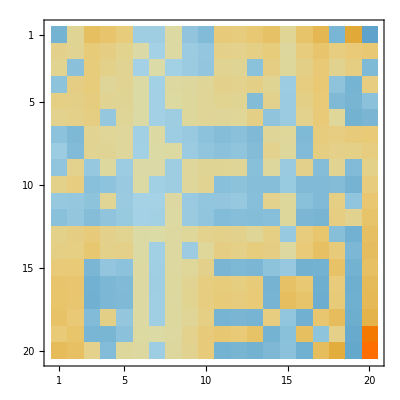

```mathematica
MatrixPlot[Transpose[Transpose[sensitivities[[All,2]][[ord1]]][[ord2]]]]
```